#### Equazioni di chiusura Manovella-Biella 17/01/2025

```mathematica
z2 = r{Cos[th2],Sin[th2]}
```

{r Cos[th2],r Sin[th2]}

```mathematica
z3 = l{Cos[th3],Sin[th3]}
```

{l Cos[th3],l Sin[th3]}

```mathematica
zOB = {xB,0}
```

{xB,0}

```mathematica
eqpos = z2 + z3  - zOB
```

{-xB+r Cos[th2]+l Cos[th3],r Sin[th2]+l Sin[th3]}

```mathematica
th31 = -ArcSin[r/l Sin[th2]]
```

-ArcSin[(r Sin[th2])/l]

```mathematica
th32 = Pi -th31
```

π+ArcSin[(r Sin[th2])/l]

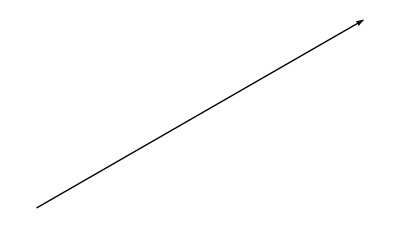

```mathematica
Graphics[Arrow[{{0,0},z2}]/. r->1/. th2->Pi/6]
```

```mathematica
z3/.th3->th31/.r->1/.l->2/.th2->Pi/6
```

{(√15)/2,-1/2}

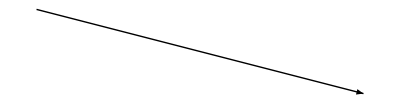

```mathematica
Graphics[Arrow[{z2,z2+z3}]/.th3->th31/.r->1/.l->2/.th2->Pi/6]
```

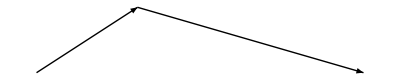

```mathematica
Show[Graphics[Arrow[{z2,z2+z3}]/.th3->th31/.r->1/.l->2/.th2->Pi/6]
,Graphics[Arrow[{{0,0},z2}]/. r->1/. th2->Pi/6]]
```

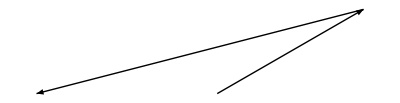

```mathematica
Show[Graphics[Arrow[{z2,z2+z3}]/.th3->th32/.r->1/.l->2/.th2->Pi/6]
,Graphics[Arrow[{{0,0},z2}]/. r->1/. th2->Pi/6]]
```

```mathematica
(*Animazione figa siuuuuum*)
```

```mathematica
Manipulate[
	Show[
	Graphics[Arrow[{{0,0},z2}]/. r->2/. th2->th22],
	   Graphics[Arrow[{z2,z2+z3}]/.th3->th31/.r->2/.l->1/.th2->th22],
		PlotRange->{{-1.5,3.5},{-1.5, 3.5}}],
			{th22,0,2Pi}]
```

```mathematica
(*quando arrivo alla condizione limite, la catena è rotta, il software dà output errore*)
```

```mathematica
(*le eq_pos devono essere considerate tempo-varianti*)
```

```mathematica
eqpost = eqpos /.th2->th2[t]/.th3->th3[t]/.xB->xB[t]
```

{r Cos[th2[t]]+l Cos[th3[t]]-xB[t],r Sin[th2[t]]+l Sin[th3[t]]}

```mathematica
{r Cos[th2[t]]+l Cos[th3[t]]-xB[t],r Sin[th2[t]]+l Sin[th3[t]]}
```

{r Cos[th2[t]]+l Cos[th3[t]]-xB[t],r Sin[th2[t]]+l Sin[th3[t]]}

```mathematica
x = th2[t] (*variabile indipendente*)
```

th2[t]

```mathematica
y = {xB[t],th3[t]} (*variabile dipendente*)
```

{xB[t],th3[t]}

```mathematica
eqvel = D[eqpost,t]
```

{-r Sin[th2[t]] th2'[t]-l Sin[th3[t]] th3'[t]-xB'[t],r Cos[th2[t]] th2'[t]+l Cos[th3[t]] th3'[t]}

```mathematica
Normal[CoefficientArrays[{a u+b v-c,d u+e v-f},{u,v}]] (*la prima uscita è il termine noto, la seconda i coeff*)
```

{{-c,-f},{{a,b},{d,e}}}

```mathematica
fx = Flatten[Normal[CoefficientArrays[eqvel,D[x,t]]][[2]]]
```

{-r Sin[th2[t]],r Cos[th2[t]]}

```mathematica
fy= Normal[CoefficientArrays[eqvel,D[y,t]]][[2]]
```

{{-1,-l Sin[th3[t]]},{0,l Cos[th3[t]]}}

```mathematica
fx //MatrixForm
```

(-r Sin[th2[t]]
r Cos[th2[t]])

```mathematica
fy //MatrixForm
```

(-1 | -l Sin[th3[t]]
0 | l Cos[th3[t]])

```mathematica
ydot = -Inverse[fy].fx  D[x,t]
```

{(-r Sin[th2[t]]+r Cos[th2[t]] Tan[th3[t]]) th2'[t],-(r Cos[th2[t]] Sec[th3[t]] th2'[t])/l}

```mathematica
xBdot = ydot[[1]]
```

(-r Sin[th2[t]]+r Cos[th2[t]] Tan[th3[t]]) th2'[t]

```mathematica
th3dot = ydot[[2]]
```

-(r Cos[th2[t]] Sec[th3[t]] th2'[t])/l

```mathematica
xBdotN = xBdot /.th3[t]->th31/.th2'[t]-> (2π/(60/(2*11500)))/.th2[t]->th2/.r->(60.8 10^(-3)/2)/.l->110 10^(-3)
```

2300/3 π (-0.0304 Sin[th2]-(0.00840145 Cos[th2] Sin[th2])/(√(1-0.0763769 Sin[th2]^2)))

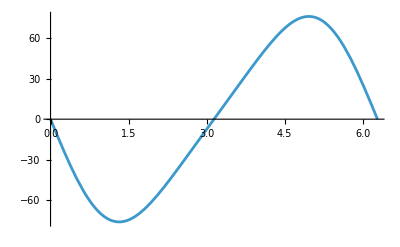

```mathematica
Plot[xBdotN,{th2,0,2π}]
```

```mathematica
xBdotN = xBdot /.th3[t]->th31/.th2'[t]-> (2π/(60/(2*11500)))/.th2[t]->th2/.r->(60.8 10^(-3)/2)/.l->110 10^(-3)/.th2->2π/(60/(2*11500))t
```

2300/3 π (-0.0304 Sin[(2300 π t)/3]-(0.00840145 Cos[(2300 π t)/3] Sin[(2300 π t)/3])/(√(1-0.0763769 Sin[(2300 π t)/3]^2)))

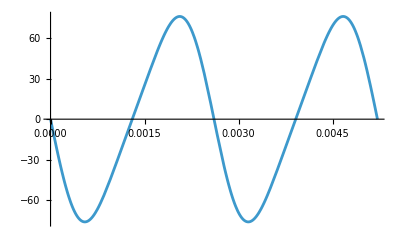

```mathematica
Plot[xBdotN,{t,0,(60/11500)}]
```

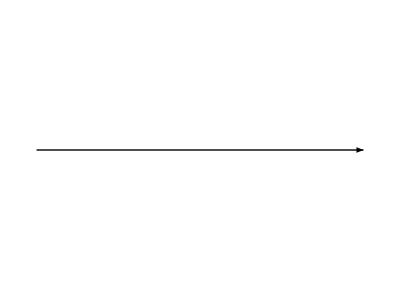

```mathematica
Graphics[Arrow[{{0,0},{r,0}}]/.r->1]
```

```mathematica
th4 = th3 - th2/.th3->th31
```

-th2-ArcSin[(r Sin[th2])/l]

-th2-ArcSin[(r Sin[th2])/l]

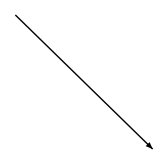

```mathematica
-th2-ArcSin[(r Sin[th2])/l]
Show[Graphics[Arrow[{{1,0},{1,0}+2{Cos[th4],Sin[th4]}/.r->1/.l->2/.th2->π/6}]]]
```

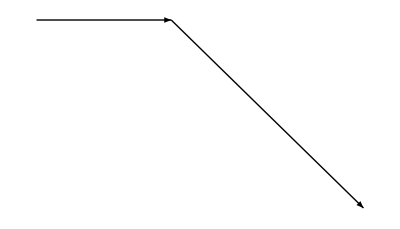

```mathematica
Show[Graphics[Arrow[{{0,0},{r,0}}]/.r->1]
,Graphics[Arrow[{{1,0},{1,0}+2{Cos[th4],Sin[th4]}/.r->1/.l->2/.th2->π/6}]]]
```

```mathematica
Manipulate[Show[Graphics[Arrow[{{0,0},{1,0}}]],
		Graphics[
		Arrow[
		{{1,0},{1,0}+2{Cos[th4],Sin[th4]}/.r->1/.l->2/.th2->th22}]],
			PlotRange->{{-1.5,3.5},{-1.5, 3.5}}],
				{th22,0,2Pi}]
```